## Population Dynamics incorporating TPCs and Autocorrelated Thermal Environments

Use this notebook to generate (or import) temperature time series, vary their levels of temporal autocorrelation, calculate the subsequent population dynamics for a population with a given thermal performance curve, and plot the results as shown in manuscript Fig 4.

### Background Functions

Run this section once. Here, we define functions for varying the level of autocorrelation in a sequence created from a set distribution of temperatures (cmplx, SpecSynFourier, Mimic1), for a thermal performance curve arising from the instantaneous temperature-dependence of population birth and death rates (gain, loss, r), and for modeling population dynamics using the r-α formulation of the logistic growth model (nt).

```mathematica
(*functions for spectral synthesis & spectral mimicry*)
cmplx[mod_,arg_]:=ExpToTrig[mod Exp[I arg]];

SpecSynFourier[γ_,Nobs_,μ_:0,σ_:1,seed_:0]:=Module[{
phase,f,vec},
If[seed==0,SeedRandom[],SeedRandom[seed]];
phase=RandomReal[{0,2Pi},Nobs];
f=Range[1/Nobs,1,1/Nobs];
vec=InverseFourier[Join[{0+0I},Table[cmplx[1/(f[[i]]^(γ/2)),phase[[i]]],{i,1,(Nobs-1)}]],FourierParameters->{-1,1}];
Standardize[Re[vec]]*σ+μ];

Mimic1[x_,z_]:=Module[{y},
y=x;
Do [y[[Ordering[z,i][[i]]]]=x[[i]],{i,1,Length[x]}];
y];

(*TPC functions and parameterization; note that any TPC can be swapped in for this r[T] function, though it should be one that includes negative growth rates*)
gain[T_]:=Exp[-((T-TI)^2)/β];
loss[T_]:=ma Exp[mb T]+mc;
r[T_]:=gain[T]-loss[T]; 

(*population dynamics function (r-α model of logistic growth)*)
nt[t_,ntlast_]:=(r[Z[[t]]]Exp[r[Z[[t]]] ])/((r[Z[[t]]]/ntlast-α)+α Exp[r[Z[[t]]]]);
```

### Simulations

Use this code to choose temperature distributions and simulate the subsequent population dynamics under assumptions of averaging, white noise, and red noise. Alternatively, temperature time series can be imported (using the commented out code) to recreate the exact published figure or to simulate dynamics over specific series. For meteorological data, code to incorporate diurnal and seasonal trends under different levels of autocorrelation is available at https://doi.org/10.5281/zenodo.17728683 (and see Robey & Vasseur 2026).

```mathematica
(*TPC parameterization*)
TI=29; β=180; 
ma=0.000005;mb=0.4;mc=0.05;
α=.001;

(*choose thermal regimes*)
μTvals=Range[25,25,1]; (*Mean temp*)
σTvals=Range[2.75,2.75,1]; (*St dev of temp*)
(*OR import thermal regimes directly*)
(*directory="IMPORTLOCATION";
Import[directory<>"data1.csv","CSV"];
Import[directory<>"data2.csv","CSV"];*)

(*simulation params*)
tmax=1000;
maxsims=1;

(*time series 1: abundance under average conditions*)
W=ConstantArray[0,{Length[μTvals],Length[σTvals],tmax}];
Do[W[[i,j,k]]=InverseCDF[NormalDistribution[μTvals[[i]],σTvals[[j]]],k*(1/tmax)],{i,1,Length[μTvals]},{j,1,Length[σTvals]},{k,1,tmax-1}]
Do[W[[i,j,tmax]]=InverseCDF[NormalDistribution[μTvals[[i]],σTvals[[j]]],(tmax-.5)*(1/tmax)],{i,1,Length[μTvals]},{j,1,Length[σTvals]}];

(*set initial pop size to mean pop size for each parameter set*)
ninit=ConstantArray[0,{Length[μTvals],Length[σTvals]}];
Do[ninit[[i,k]]=(Mean[Table[r[W[[i,k,j]]],{j,1,tmax}]])/α,{k,1,Length[σTvals]},{i,1,Length[μTvals]}]

lt25=ConstantArray[ninit[[1,1]],tmax];

(*time series 2: abundance under white noise conditions*)
γvals=Range[0,0,0];  (*Autocorrelation level*)

(*set initial population size to the average expected abundance given the temp distribution*)
W=ConstantArray[0,{Length[μTvals],Length[σTvals],tmax}];
Do[W[[i,j,k]]=InverseCDF[NormalDistribution[μTvals[[i]],σTvals[[j]]],k*(1/tmax)],{i,1,Length[μTvals]},{j,1,Length[σTvals]},{k,1,tmax-1}]
Do[W[[i,j,tmax]]=InverseCDF[NormalDistribution[μTvals[[i]],σTvals[[j]]],(tmax-.5)*(1/tmax)],{i,1,Length[μTvals]},{j,1,Length[σTvals]}];

ninit=ConstantArray[0,{Length[μTvals],Length[σTvals]}];
Do[ninit[[i,k]]=(Mean[Table[r[W[[i,k,j]]],{j,1,tmax}]])/α,{k,1,Length[σTvals]},{i,1,Length[μTvals]}]

(*initialize array to store extinction times; =tmax if not extinct*)
extTime=ConstantArray[tmax,{Length[γvals],Length[μTvals],Length[σTvals],maxsims}];
(*initialize array to store population sizes*)
p1=ConstantArray[0,{Length[γvals],Length[μTvals],Length[σTvals],maxsims,tmax}];
Do[p1[[i,j,m,l,1]]=ninit[[j,m]],{l,1,maxsims},{m,1,Length[σTvals]},{j,1,Length[μTvals]},{i,1,Length[γvals]}]

temps1=ConstantArray[0,{Length[μTvals],Length[σTvals]}];

SetSharedVariable[p1,extTime];
Do[γ=γvals[[i]];
μT=μTvals[[j]];
σT=σTvals[[m]];

X=SpecSynFourier[γ,tmax];
Z=Mimic1[W[[j,m]],X];
envt=Interpolation[Z,InterpolationOrder->0];

temps1[[j,m]]=Z;

Do[p1[[i,j,m,l,k]]=nt[k,p1[[i,j,m,l,k-1]]];
If[p1[[i,j,m,l,k]]<1,extTime[[i,j,m,l]]=k;
Break[]];,{k,2,tmax}],

{l,1,maxsims},{m,1,Length[σTvals]},{j,1,Length[μTvals]},{i,1,Length[γvals]}]

data1={p1[[1,1,1,1]]};

(*time series 2: abundance under red noise conditions (repeats above with higher level of autocorrelation) *)
γvals=Range[1,1,1];

W=ConstantArray[0,{Length[μTvals],Length[σTvals],tmax}];
Do[W[[i,j,k]]=InverseCDF[NormalDistribution[μTvals[[i]],σTvals[[j]]],k*(1/tmax)],{i,1,Length[μTvals]},{j,1,Length[σTvals]},{k,1,tmax-1}]
Do[W[[i,j,tmax]]=InverseCDF[NormalDistribution[μTvals[[i]],σTvals[[j]]],(tmax-.5)*(1/tmax)],{i,1,Length[μTvals]},{j,1,Length[σTvals]}];

ninit=ConstantArray[0,{Length[μTvals],Length[σTvals]}];
Do[ninit[[i,k]]=(Mean[Table[r[W[[i,k,j]]],{j,1,tmax}]])/α,{k,1,Length[σTvals]},{i,1,Length[μTvals]}]

(*initialize array to store extinction times; =tmax if not extinct*)
extTime=ConstantArray[tmax,{Length[γvals],Length[μTvals],Length[σTvals],maxsims}];
(*initialize array to store population sizes*)
p1=ConstantArray[0,{Length[γvals],Length[μTvals],Length[σTvals],maxsims,tmax}];
Do[p1[[i,j,m,l,1]]=ninit[[j,m]],{l,1,maxsims},{m,1,Length[σTvals]},{j,1,Length[μTvals]},{i,1,Length[γvals]}]

temps2=ConstantArray[0,{Length[μTvals],Length[σTvals]}];

SetSharedVariable[p1,extTime];
Do[γ=γvals[[i]];
μT=μTvals[[j]];
σT=σTvals[[m]];

X=SpecSynFourier[γ,tmax];
Z=Mimic1[W[[j,m]],X];
envt=Interpolation[Z,InterpolationOrder->0];

temps2[[j,m]]=Z;

Do[p1[[i,j,m,l,k]]=nt[k,p1[[i,j,m,l,k-1]]];
If[p1[[i,j,m,l,k]]<1,extTime[[i,j,m,l]]=k;
Break[]];,{k,2,tmax}],

{l,1,maxsims},{m,1,Length[σTvals]},{j,1,Length[μTvals]},{i,1,Length[γvals]}]

data2={p1[[1,1,1,1]]};

(*export generated time and abundance time series*)
Export[directory<>"temps1.m",temps1,"MX"];
Export[directory<>"data1.m",data1,"MX"];
Export[directory<>"temps2.m",temps2,"MX"];
Export[directory<>"data2.m",data2,"MX"];

Export[directory<>"temps1.csv",temps1,"CSV"];
Export[directory<>"data1.csv",data1,"CSV"];
Export[directory<>"temps2.csv",temps2,"CSV"];
Export[directory<>"data2.csv",data2,"CSV"];
```

### Plotting

Generate and download Fig 4 subfigures (combined and annotated using Adobe Illustrator 2024).

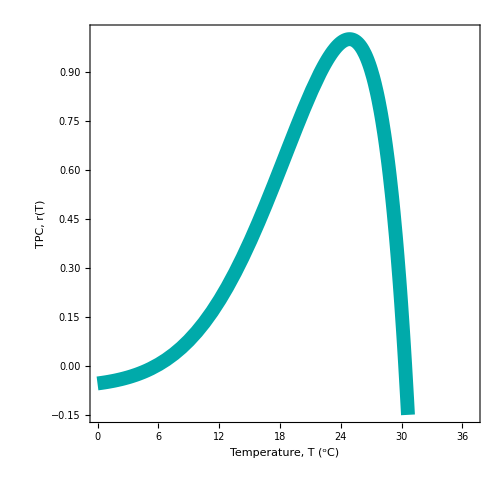

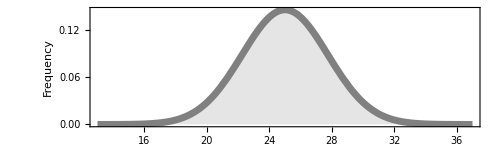

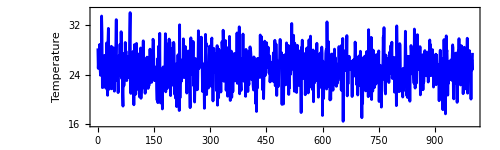

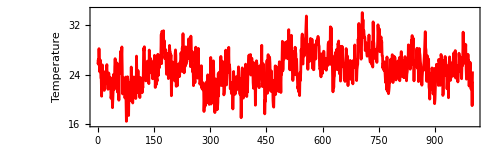

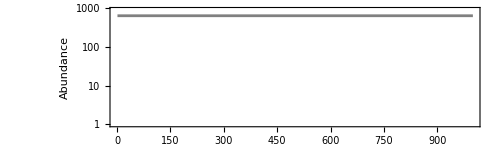

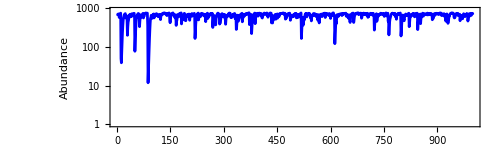

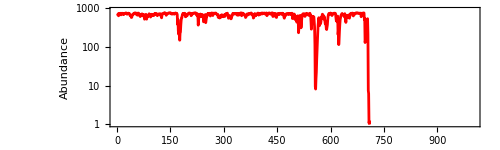

```mathematica
(*if recreating exact figure, import files first*)
temps1=Import[directory<>"temps1.m","MX"];
data1=Import[directory<>"data1.m","MX"];
temps2=Import[directory<>"temps2.m","MX"];
data2=Import[directory<>"data2.m","MX"];

(* (a) TPC *)
TPChist=Show[Plot[r[T]/.755,{T,0,37},PlotStyle->{Thickness[0.02],Darker[Cyan]},PlotRange->{{0,37},{-.15,1.02}},Frame->{True,True,False,True},FrameStyle->24,FrameLabel->{"Temperature, T (^oC)",Style["TPC, r(T)",Darker[Cyan]],None,None},LabelStyle->Directive[Black],FrameTicks->{Automatic,{0,0.25,0.5,0.75,1},None,Automatic},ImageSize->500,AspectRatio->1]]

(* (b-d) temp distribution and series*)
framesize=20;
sublabel=24;

series1=Plot[PDF[NormalDistribution[25,2.75],x],{x,13,37},
PlotStyle->{Thickness[0.01],Gray},PlotRange->Full,Filling->Axis,Frame->{True,True,False,False},FrameTicks->{{},{},{},{}},FrameStyle->framesize,FrameLabel->{"Temperature","Frequency"},
LabelStyle->Directive[Black],ImageSize->500,AspectRatio->.3]
series2=ListLinePlot[{temps1[[1,1]]},PlotStyle->{Blue},PlotRange->{{0,tmax},{16,34.5}},Frame->{True,True,False,False},FrameStyle->framesize,FrameLabel->{"Time","Temperature"},LabelStyle->Directive[Black],ImageSize->500,AspectRatio->.3]
series3=ListLinePlot[{temps2[[1,1]]},PlotStyle->{Red},PlotRange->{{0,tmax},{16,34.5}},Frame->{True,True,False,False},FrameStyle->framesize,FrameLabel->{"Time","Temperature"},LabelStyle->Directive[Black],ImageSize->500,AspectRatio->.3]

(* (e-g) population dynamics*)
pop1=ListLinePlot[lt25,ScalingFunctions->{"Linear","Log"},PlotStyle->{Gray},PlotRange->{{0,tmax},{1,900}},Frame->{True,True,False,False},FrameStyle->framesize,FrameTicksStyle->Directive[FontSize->16],FrameLabel->{"Time","Abundance"},LabelStyle->Directive[Black],ImageSize->500,AspectRatio->.3]
pop2=ListLinePlot[data1,ScalingFunctions->{"Linear","Log"},PlotStyle->{Blue},PlotRange->{{0,tmax},{1,900}},Frame->{True,True,False,False},FrameStyle->framesize,FrameTicksStyle->Directive[FontSize->16],FrameLabel->{"Time","Abundance"},LabelStyle->Directive[Black],ImageSize->500,AspectRatio->.3]
pop3=ListLinePlot[data2,ScalingFunctions->{"Linear","Log"},PlotStyle->{Red},PlotRange->{{0,tmax},{1,900}},Frame->{True,True,False,False},FrameStyle->framesize,FrameTicksStyle->Directive[FontSize->16],FrameLabel->{"Time","Abundance"},LabelStyle->Directive[Black],ImageSize->500,AspectRatio->.3]

Export[directory<>"TPChist.pdf",TPChist,ImageResolution->1000];
Export[directory<>"temps1.pdf",series1,ImageResolution->1000];
Export[directory<>"temps2.pdf",series2,ImageResolution->1000];
Export[directory<>"temps3.pdf",series3,ImageResolution->1000];
Export[directory<>"pop1.pdf",pop1,ImageResolution->1000];
Export[directory<>"pop2.pdf",pop2,ImageResolution->1000];
Export[directory<>"pop3.pdf",pop3,ImageResolution->1000];
```